```mathematica
f[x_]:=a Sin[b x]+c Cos[d x]+Cos[x]+4.5
a=1.4
b=3
c=1.2
d=4.5
N[Solve[f'[x+4.077]==0&&x>0&&x<5,x, Reals]]
x0=1.1
x1=2.031982161048468
x2=3.690200140461272
x3=0.8924904834689227
off=0.2
s=15
s1=15
Plot[f[x+4.077],{x,0,5}, Ticks->None, Epilog->{Point[{x0,f[x0+4.077]}],Text[Style["C",s],{x0,f[x0+4.077]+off},{0,-1}],Point[{x1,f[x1+4.077]}],Text[Style["C_1",s],{x1,f[x1+4.077]+off},{0,-1}],Point[{x2,f[x2+4.077]}],Text[Style["C_0",s],{x2,f[x2+4.077]+off},{0,-1}],Point[{x3,f[x3+4.077]}],Text[Style["C_2",s],{x3,f[x3+4.077]+off},{0,-1}]}, FrameLabel->{Style["Configuraciones",s1], Style["F",s1]}]
```

## Hexagonos

0.06

-Graphics-

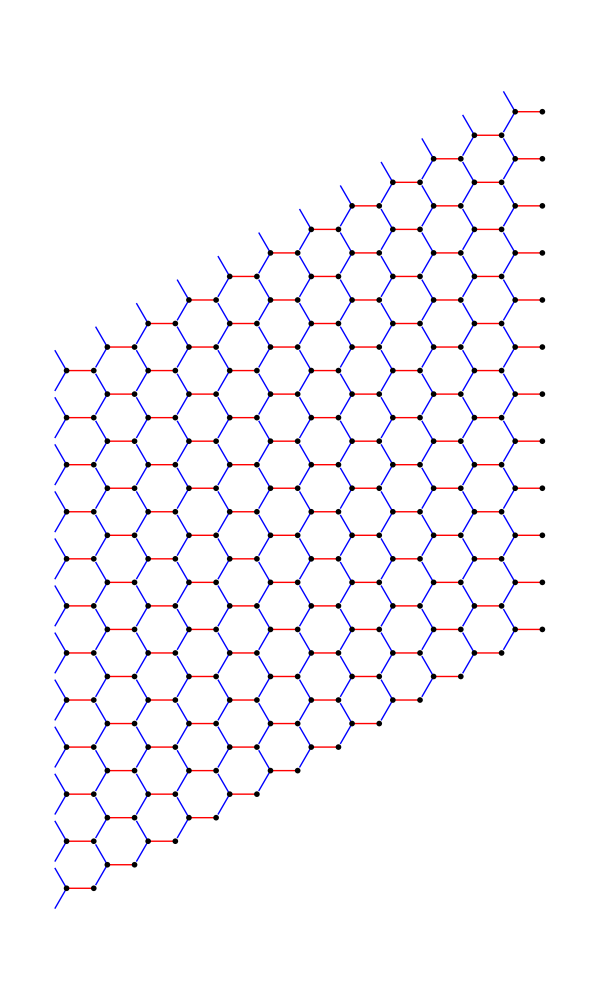

```mathematica
tam=0.06
unitCell[x_,y_]:={Red,Line[{{x,y},{x+2/3 Sin[120 Degree],y}}],Blue,Line[{{x,y},{x-Sin[30 Degree]/2,y+Cos[30 Degree]/2}}],Blue,Line[{{x,y},{x-Sin[30 Degree]/2,y-Cos[30 Degree]/2}}],Black,Disk[{x,y},tam],Black,Disk[{x+2/3 Sin[120 Degree],y},tam]}
Graphics[unitCell[0,0],ImageSize->100]
Graphics[Block[{unitVectA={Sin[60Degree],Cos[60Degree]},unitVectB={0,1}},Table[unitCell@@(unitVectA j+unitVectB k),{j,-12,-1},{k,1,12}]],ImageSize->600]
```

Cuadrados

0.06

-Graphics-

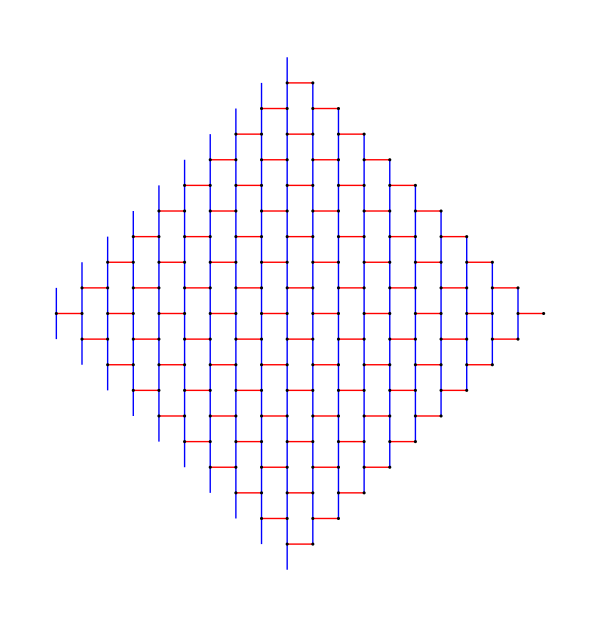

```mathematica
tam=0.06
unitCell2[x_,y_]:={Red,Line[{{x,y},{x+1,y}}],Blue,Line[{{x,y},{x,y+1}}],Blue,Line[{{x,y},{x,y-1}}],Black,Disk[{x,y},tam],Black,Disk[{x+1,y},tam]}
Graphics[unitCell2[0,0],ImageSize->100]
Graphics[Block[{unitVectA={-1,1},unitVectB={-1,-1}},Table[unitCell2@@(unitVectA j+unitVectB k),{j,-10,-1},{k,1,10}]],ImageSize->600]
```

## Archivos y fit

FittedModel[0.600838-0.356011 Tanh[6.20103-10.1247 x]-0.0399776 Tanh[8.21447-10.1247 x]]

FittedModel[0.575728-0.0555723 Tanh[1.35708-11.0945 x]-0.358387 Tanh[2.94956-11.0945 x]]

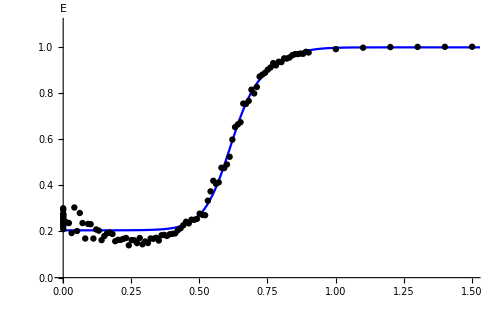

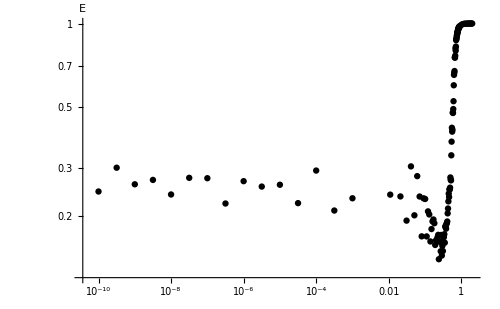

0.613216

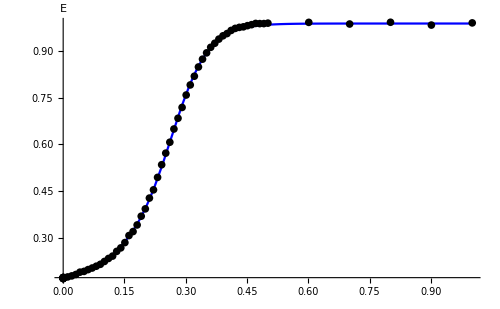

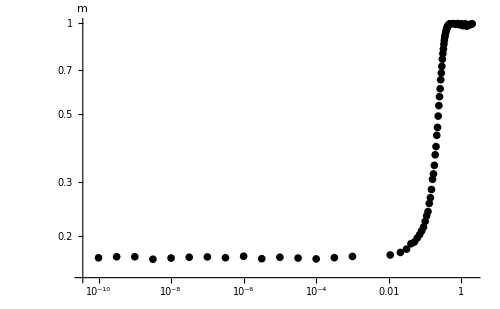

0.263817

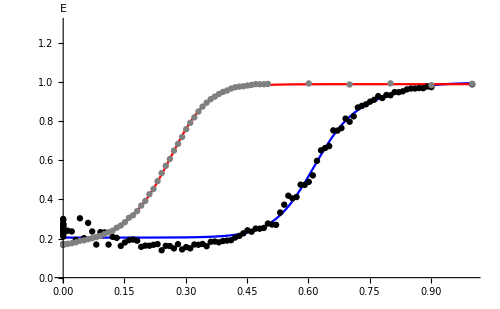

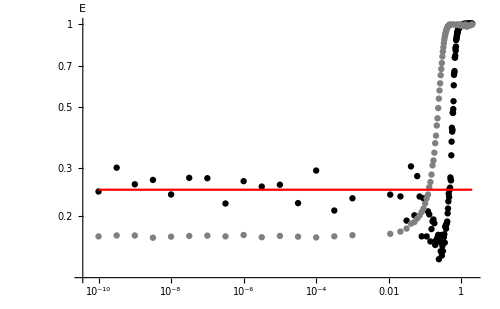

```mathematica
data=Import["C:\\Users\\pcard\\OneDrive\\4.ba\\TFG\\Python TFG\\IsingModel\\QAhexmagnetizacion821.dat"];
data2=Import["C:\\Users\\pcard\\OneDrive\\4.ba\\TFG\\Python TFG\\IsingModel\\hexmagnetizacion82.dat"];
base=a+b Tanh[c x-d]+e Tanh[c x -i];
l=Length[data];
s=500;
n=8;
l2=Length[data2];
absdata=Table[{data[[i]][[1]],Abs[data[[i]][[2]]]/(0.001*n*n)},{i,1,l}];
absdata2=Table[{data2[[i]][[1]],Abs[data2[[i]][[2]]]},{i,1,l2}];
f=NonlinearModelFit[absdata,base,{a,b,c,d,e,i},x]
f2=NonlinearModelFit[absdata2,base,{a,b,c,d,e,i},x]
g=D[f,{x,2}];
g2=D[f2,{x,2}];
linea=Table[{data[[i]][[1]],2/n},{i,1,l}];


plot=Show[Plot[f[x],{x,0,2},PlotRange->{{0,1.5},{0,1.1}},PlotStyle->Blue,AxesLabel->{Style["",Large], Style["E",Large]}],ListPlot[absdata,PlotStyle->Black], ImageSize->s]
Show[ListLogLogPlot[absdata,PlotStyle->{Black},AxesLabel->{Style["",Large], Style["E",Large]},ImageSize->s]]
k1=NSolve[f''[x]==0,x,Reals];
K1=x/. k1[[1]]

plot2=Show[Plot[f2[x],{x,0,1},PlotRange->Full,PlotStyle->Blue,AxesLabel->{Style["",Large], Style["E",Large]}],ListPlot[absdata2,PlotStyle->Black], ImageSize->s]
Show[ListLogLogPlot[absdata2,PlotStyle->{Black},AxesLabel->{Style["",Large], Style["m",Large]},ImageSize->s]]
k2=NSolve[f2''[x]==0,x,Reals];
K2 = x/.k2[[1]]

plot2=Show[Plot[{f[x],f2[x]},{x,0,1},PlotRange->{{0,1},{0,1.3}},PlotStyle->{Blue, Red},AxesLabel->{Style["",Large], Style["E",Large]}],ListPlot[{absdata,absdata2},PlotStyle->{Black, Gray}], ImageSize->s]
Show[ListLogLogPlot[{absdata,absdata2}, PlotRange->Full,PlotStyle->{Black, Gray},AxesLabel->{Style["",Large], Style["E",Large]},ImageSize->s], ListLogLogPlot[linea, PlotStyle->Red,Joined->True], ImageSize->s]
```